```mathematica
kR = (3*2/3+4*1/3)/(4 * 2/6.)
```

2.5

```mathematica
dI[k_, L_] := (0.92 k)/(3 + 4 * k) L
```

```mathematica
dR = dI[2.5, 6]
```

1.06154

```mathematica
dL = dI[1.5, 6]
```

0.92

```mathematica
Leff = 6 - dR - dL
```

4.01846

```mathematica
Mpos = 100 * Leff^2/8;
ML = 100/2*dL *(dL + Leff);
MR = 100/2*dR *(dR + Leff);
{ML, Mpos, MR}
```

{227.169,201.85,269.631}

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {3}, {4, 6, 3},300,
buildingBeamUniformLoadList -> { {1, 2}-> 100},
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 2},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> False,
{1, 4} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {_-> "fixed"},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {3 -> "fixed"},
buildingFactorMomentDiagrams -> 0.002,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

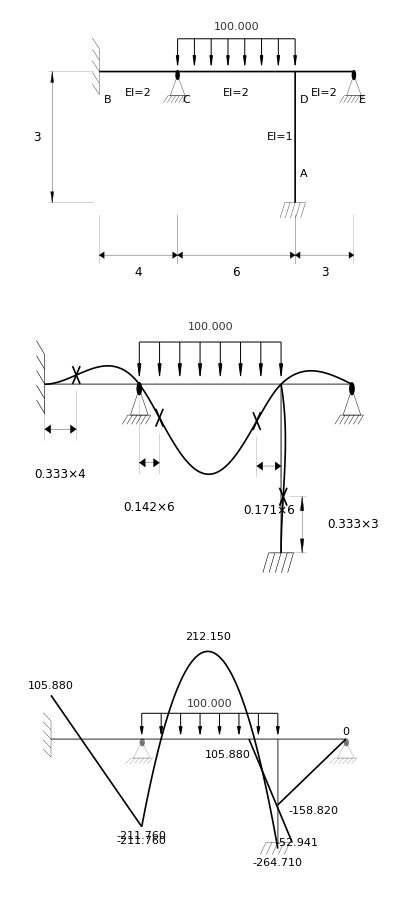

```mathematica
{227.1692307692308,201.85041420118347,269.63076923076926}
```

```mathematica
(269.6-264.7)/264.7*100
```

1.85115

```mathematica
ML/2
```

113.585

```mathematica
(3*2/3)/(3*2/3+4*1/3){1, 270.}
```

{3/5,162.}

```mathematica
(4*1/3)/(3*2/3+4*1/3){1, 270.}
```

{2/5,108.}